```mathematica
SOI=Import["/users/pp/Desktop/soi.txt", "table"];
TSID=Import["/users/pp/Desktop/tsi.txt", "table"];
QBO=Import["/users/pp/Desktop/qbo20.txt", "table"];
QBO70=Import["/users/pp/Desktop/qbo.txt", "table"];
CW=Import["/users/pp/Desktop/cw.txt", "table"];
CW1=Import["/users/pp/Desktop/cw1_1930.txt", "table"];
CW0=Import["/users/pp/Desktop/cw1.txt", "table"];
NINO34=Import["/users/pp/Desktop/nino34ke.txt", "table"];
tahiti=Import["/users/pp/Desktop/tahiti.txt", "table"];
darwin=Import["/users/pp/Desktop/darwin0.txt", "table"];
```

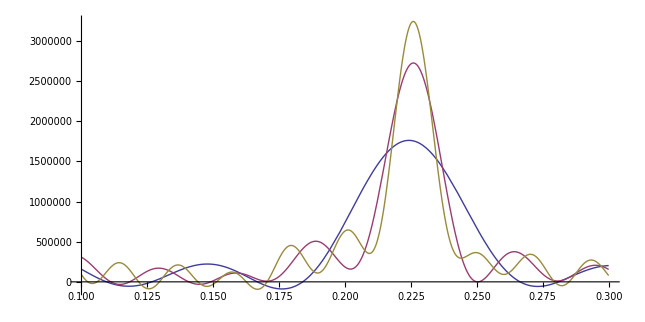

2.49333

```mathematica
QBOT = Table[{QBOM[[i,1]], Q[[i]]},{i,12*27,12*61.25+1, 1}];      
Plot[Evaluate@Table[PowerSpectralDensity[QBOT,ω,i],{i,100,300,100}],{ω,0.1,0.3},PlotRange->All,AspectRatio->0.5] 
2*Pi/.21/12
```

{char t,3.68961,0.0387705, Years from,1880.75,to,2013.33,CC,91.9948,93.5089,1.51411}

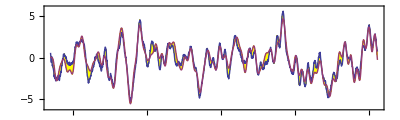

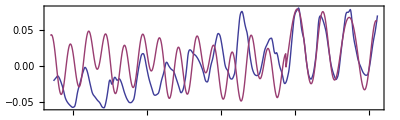

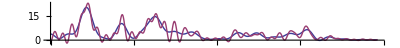

5.23599

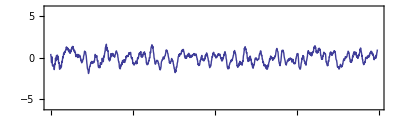

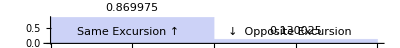

```mathematica
QB=2.696; qbo[x_] :=  Cos[QB*(x+0.24*Sin[0.523*x+2.82]-0.07*Sin[0.12*x+0.2])+1.44] ; 
CW =0.9698; cw[x_] := Sin[CW*(x+2.)+ 0.119*Sin[0.36*(x+6.8)] +0.5] *(1+0.31*Sin[0.093*x-0.2]) ;  
sigmoid[x_] := 1/(1+Exp[6*(x-94.0)]); 
HALE:=0.59; HALE2:=0.596;
tsi[x_] := +1.12*((sigmoid[x])*0.62*(2.7*Cos[HALE*(x-0.11)] + 0.7*Cos[HALE/2*(x-5.7)]+0.18*Cos[HALE/3*(x+3.8)]) +
                   (1-sigmoid[x])*0.99*(3.12*Cos[HALE2*(x-1.29)]+0.55*Cos[HALE/2*(x-7.0)])) +  
             2.42*Cos[2*Pi*x/153.1-1.0] +0.62*Cos[2*Pi*x/9.57+1.5] + 0.55*Cos[2*Pi*x/105.0+0.4] + 0*0.39*Cos[2*Pi*x/12.9+2.5]; 
Window = 9;  
R = MeanFilter[MeanFilter[(1*MeanFilter[darwin[[All,2]],Window])-(1*MeanFilter[tahiti[[All,2]],Window]),Window-2],Window-4];
STRT=9; STRTY=1880+STRT/12;LNGTH=1600; ENDY=1880+LNGTH/12; 
QBW=2.331;   TSP = 21.97;  TR1 = 99.4; TR = 99.4;  CF = 2.9;  OSC := 9.08;  CWP := 6.47;  
TSI[x_] := Cos[2*Pi/(TSP/3)*x+2.5] * If[x<TR, 1.87, 0.6] - 0.35*Cos[2*Pi/TSP*x+0.2] +
           If[x<TR, 0*0.5*Cos[2*Pi/17*x-0.2] + 0.2*tsi[x-2]-1.3*Cos[2*Pi/TSP*x+3.3],   -0.92*tsi[x-2.6]];
Hill[x_] := CF+0.25*tsi[x+0.48]; 
Tide9[x_] := 0.44*(Cos[2*Pi/OSC*x+4.57]-0.12*Cos[4*Pi/OSC*x+2.9]+0.19*Cos[Pi/(2*OSC)*x+3.5])-0.25*Cos[2*Pi*x/(3*OSC)-0.5];
Osc[x_] := 1.08*Tide9[x-0.01]-0.22*Cos[2*Pi/8.85*x+3] -0.11*Cos[2*Pi/8*x+5.5] +0.06*Cos[2*Pi/5*x+0.7] ;
qbw[x_] := +0.42*Cos[2*Pi/(QBW*3)*x+2.2]+0.22*Cos[2*Pi/QBW*x+2.5] -0*0.09*Cos[2*Pi/2.119*x-0.3] + 
                                     If[x<TR,-0.21*Cos[2*Pi/2.91*x-0.4],  -0.53*Cos[2*Pi/2.458*x-0.96]];
cwb[x_] := -0.6*cw[x+0.12]+0.28*cw[x/2+1.4] + 0.3*Cos[2*Pi/5.8*x+1.4];  
RHS[x_] := 3.0*qbw[x-0.01]+2.89*cwb[x-0.23]-1.18*Cos[2*Pi/48*x+1]-5.9*Osc[x-1.2] + 1.1*TSI[x] ;  

lhs=Table[{1880.0+x,  12*12*(2*R[[x*12]]-R[[x*12+1]]-R[[x*12-1]])-Hill[x]*R[[x*12]] - 0.08*(R[[x*12]])^3},{x,STRT/12,LNGTH/12+0, 1/12}];     
rhs=Table[{1880.0+x, -0.55*RHS[x+0.8]},  {x,STRT/12,LNGTH/12+0, 1/12}];     
OldCC = NewCC; NewCC = 100*Correlation[lhs,rhs][[2,2]];  Var = Variance[lhs]-Variance[rhs];
Print[{"char t",2*Pi/Sqrt[CF],Var[[2]]," Years from",N[STRTY],"to",N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{lhs,rhs},PlotRange->{-6,6},Frame->True,Axes->True, Filling->{1->{{2},Yellow}}, PlotLegends->{"lhs","rhs"},AspectRatio->0.3] 
qbww = Table[{1880+i/12, (3*qbw[i/12])},{i,STRT,LNGTH,1}];
tsiw = Table[{1880+i/12, (0.017*TSI[i/12+3])},{i,STRT,LNGTH,1}];
ListLinePlot[{TSIT,tsiw},  AspectRatio->0.3, Frame->True, Axes->False, PlotLegends->{"qbw","tsi"}]
SDIF = lhs[[All,2]]-rhs[[All,2]];  
Plot[Evaluate@Table[PowerSpectralDensity[SDIF,ω,i],{i,400,800,400}],{ω,0,π/10},PlotRange->All,AspectRatio->0.1] 
2*Pi/0.1/12
ListLinePlot[{SDIF},PlotRange->{-6,6},Frame->True,Axes->True, PlotLegends->{"diff"},AspectRatio->0.3] 
SBIN = Abs[Sign[lhs[[All,2]]]- Sign[rhs[[All,2]]]]/2; 
Histogram[SBIN, Automatic, "Probability", LabelingFunction->Above, AspectRatio->0.05,  ChartLabels->Placed[{"Same Excursion ↑              ↓  Opposite Excursion"},Bottom]]
```

{char t,3.40254,0.186736, Years from,1880.75,to,2013.33,CC,85.8743,85.8743,0.}

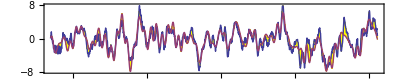

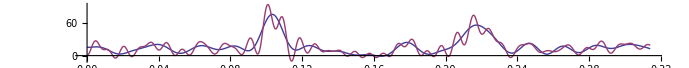

2.42407

```mathematica
CW =0.9698; cw[x_] := Sin[CW*(x+2.)+ 0.119*Sin[0.36*(x+6.8)] +0.5] *(1+0.31*Sin[0.093*x-0.2]) ;  
sigmoid[x_] := 1/(1+Exp[6*(x-94.0)]); 
HALE:=0.59; HALE2:=0.596;
tsi[x_] := +1.12*((sigmoid[x])*0.62*(2.7*Cos[HALE*(x-0.11)] + 0.7*Cos[HALE/2*(x-5.7)]+0.18*Cos[HALE/3*(x+3.8)]) +
                   (1-sigmoid[x])*0.99*(3.12*Cos[HALE2*(x-1.29)]+0.55*Cos[HALE/2*(x-7.0)])) +  
             2.42*Cos[2*Pi*x/153.1-1.0] +0.62*Cos[2*Pi*x/9.57+1.5] + 0.55*Cos[2*Pi*x/105.0+0.4] + 0*0.39*Cos[2*Pi*x/12.9+2.5]; 
Window = 7;  
R = MeanFilter[MeanFilter[(1*MeanFilter[darwin[[All,2]],Window])-(1*MeanFilter[tahiti[[All,2]],Window]),Window-2],Window-4];
STRT=9; STRTY=1880+STRT/12;LNGTH=1600; ENDY=1880+LNGTH/12; 
QBW=2.333333;   TSP = 21.98;  TR1 = 99.4; TR = 99.4;  CF = 3.41;  OSC := 9.09;  CWP := 6.47;  
TSI[x_] := 1.3*Cos[2*Pi/(TSP/3)*x+2.5] -0.35*Cos[2*Pi/TSP*x+0.2] + 0.51*Cos[2*Pi/(TSP/4)*x+3.4] +
           If[x<TR,0.19*tsi[x-2]-1.5*Cos[2*Pi/TSP*x+3.3],-1.3*tsi[x-2.5]] ;
Hill[x_] := If[x<2*TR,CF, 4.2];  (*+0*.07*tsi[x+1.2]; *)
Tide9[x_] := 0.44*(Cos[2*Pi/OSC*x+4.57]-0.12*Cos[4*Pi/OSC*x+2.9]+0.19*Cos[Pi/(2*OSC)*x+3.5])-0.25*Cos[2*Pi*x/(3*OSC)-0.5];
Osc[x_] := 1.08*Tide9[x-0.01]-0.22*Cos[2*Pi/8.85*x+3] -0.11*Cos[2*Pi/8*x+5.5] +0.07*Cos[2*Pi/5*x+0.7] ;
qbo[x_] :=  Cos[2*Pi/QBW*(x+0.2*Cos[2*Pi/18.62*x+0.4])+2.9];
qbw[x_] := +0.42*Cos[2*Pi/(QBW*3)*x+2.2]+0.53*qbo[x] + If[x<2*TR,0.22*Cos[2*Pi/2.25*x-1.5]-0.17*Cos[2*Pi/2.91*x-0.8],
            -0.3*qbo[x]-0.7*Cos[2*Pi/2.457*x-0.9]];
cwb[x_] := -0.6*cw[x+0.12]+0.24*cw[x/2+1.4] + 0.3*Cos[2*Pi/5.8*x+1.4];  
RHS[x_] := If[x<TR, 3.0*qbw[x-0.05], 2.9*qbw[x-0.3]]*(1+0.2*tsi[x+1]) +
           3.0*cwb[x-0.23]-1.1*Cos[2*Pi/48*x+1]-5.8*Osc[x-1.2] + 1.1*TSI[x] ;  
lhs=Table[{1880.0+x,  12*12*(2*R[[x*12]]-R[[x*12+1]]-R[[x*12-1]])-Hill[x]*R[[x*12]] - 0.08*(R[[x*12]])^3},{x,STRT/12,LNGTH/12+0, 1/12}];     
rhs=Table[{1880.0+x, -0.71*RHS[x+0.83]},  {x,STRT/12,LNGTH/12+0, 1/12}];     
OldCC = NewCC; NewCC = 100*Correlation[lhs,rhs][[2,2]];  Var = Variance[lhs]-Variance[rhs];
Print[{"char t",2*Pi/Sqrt[CF],Var[[2]]," Years from",N[STRTY],"to",N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{lhs,rhs},PlotRange->{-8,8},Frame->True,Axes->True, Filling->{1->{{2},Yellow}}, PlotLegends->{"lhs","rhs"},AspectRatio->0.2] 
SDIF = lhs[[All,2]]-rhs[[All,2]];  
Plot[Evaluate@Table[PowerSpectralDensity[SDIF,ω,i],{i,400,800,400}],{ω,0,π/10},PlotRange->All,AspectRatio->0.1] 
2*Pi/0.216/12
(*
qbww = Table[{1880+i/12, (qbw[i/12])},{i,STRT,LNGTH,1}];
tsiw = Table[{1880+i/12, (0.17*TSI[i/12+3])},{i,STRT,LNGTH,1}];
hillw = Table[{1880+i/12, (Hill[i/12])},{i,STRT,LNGTH,1}];
ListLinePlot[{qbww,tsiw,hillw},  AspectRatio->0.3, Frame->True, Axes->False, PlotLegends->{"qbw","tsi","hill"}]
ListLinePlot[{SDIF},PlotRange->{-6,6},Frame->True,Axes->True, PlotLegends->{"diff"},AspectRatio->0.3] 
SBIN = Abs[Sign[lhs[[All,2]]]- Sign[rhs[[All,2]]]]/2; 
Histogram[SBIN, Automatic, "Probability", LabelingFunction->Above, AspectRatio->0.05,  ChartLabels->Placed[{"Same Excursion ↑              ↓  Opposite Excursion"},Bottom]]
```

{char t,3.31153,0.547399, Years from,1880.75,to,1980.,CC,87.4746,87.4836,0.00902689}

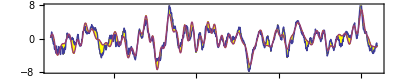

```mathematica
CW =0.9698; cw[x_] := Sin[CW*(x+2.)+ 0.119*Sin[0.36*(x+6.8)] +0.5] *(1+0.31*Sin[0.093*x-0.2]) ;  
sigmoid[x_] := 1/(1+Exp[6*(x-94.0)]); 
HALE:=0.59; HALE2:=0.596;
tsi[x_] := +1.12*((sigmoid[x])*0.62*(2.7*Cos[HALE*(x-0.11)] + 0.7*Cos[HALE/2*(x-5.7)]+0.18*Cos[HALE/3*(x+3.8)]) +
                   (1-sigmoid[x])*0.99*(3.12*Cos[HALE2*(x-1.29)]+0.55*Cos[HALE/2*(x-7.0)])) +  
             2.42*Cos[2*Pi*x/153.1-1.0] +0.62*Cos[2*Pi*x/9.57+1.5] + 0.55*Cos[2*Pi*x/105.0+0.4] + 0*0.39*Cos[2*Pi*x/12.9+2.5]; 
Window = 7;  
R = MeanFilter[MeanFilter[(1*MeanFilter[darwin[[All,2]],Window])-(1*MeanFilter[tahiti[[All,2]],Window]),Window-2],Window-4];
STRT=9; STRTY=1880+STRT/12;LNGTH=1200; ENDY=1880+LNGTH/12; 
QBW=2.333333;   TSP = 22.0;   TR = 99.4;  CF = 3.6;  OSC := 9.09;  CWP := 6.47;   DIP := 18.62; 
TSI[x_] := 1.3*Cos[2*Pi/(TSP/3)*x+2.5] -0.35*Cos[2*Pi/TSP*x+0.2] + 0.51*Cos[2*Pi/(TSP/4)*x+3.4] +
           If[x<TR,0.17*tsi[x-2]-1.7*Cos[2*Pi/TSP*x+3.3],-1.5*tsi[x-2.5]] - 0.7*Cos[2*Pi/5.24*x-1.9] ;
Hill[x_] := If[x<TR,CF, 4.5];  (*+0*.07*tsi[x+1.2]; *)
Tide9[x_] := 0.44*(Cos[2*Pi/OSC*x+4.57]-0.12*Cos[4*Pi/OSC*x+2.9]+0.19*Cos[Pi/(2*OSC)*x+3.5])-0.25*Cos[2*Pi*x/(3*OSC)-0.5];
Osc[x_] := 1.08*Tide9[x-0.01]-0.22*Cos[2*Pi/8.85*x+3] -0.06*Cos[2*Pi/8*x+5.5] +0.07*Cos[2*Pi/5*x+0.7] ;
qbo[x_] :=  Cos[2*Pi/QBW*(x+0.2*Cos[2*Pi/DIP*x+0.4])+2.9];
qbw[x_] := +0.42*Cos[2*Pi/(QBW*3)*x+2.2] +  0.53*qbo[x] + 
            0.22*Cos[2*Pi/2.25*x-1.5 +0.2*Cos[2*Pi/DIP*x+1.4] ] -
            0.17*Cos[2*Pi/2.91*x-0.8 +0.6*Cos[2*Pi/DIP*x+0.5]] -
           0.09*Cos[2*Pi/2.457*x-0.8];
cwb[x_] := -0.6*cw[x+0.12]+0.24*cw[x/2+1.4] + 0.3*Cos[2*Pi/5.8*x+1.4];  
RHS[x_] := 3.0*qbw[x-0.1]*(1+0.19*tsi[x+1]) +
           3.0*cwb[x-0.23]-1.1*Cos[2*Pi/48*x+1]-5.8*Osc[x-1.2] + 1.1*TSI[x] ;  
lhs=Table[{1880.0+x,  12*12*(2*R[[x*12]]-R[[x*12+1]]-R[[x*12-1]])-Hill[x]*R[[x*12]] - 0.08*(R[[x*12]])^3},{x,STRT/12,LNGTH/12+0, 1/12}];     
rhs=Table[{1880.0+x, -0.71*RHS[x+0.83]},  {x,STRT/12,LNGTH/12+0, 1/12}];     
OldCC = NewCC; NewCC = 100*Correlation[lhs,rhs][[2,2]];  Var = Variance[lhs]-Variance[rhs];
Print[{"char t",2*Pi/Sqrt[CF],Var[[2]]," Years from",N[STRTY],"to",N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{lhs,rhs},PlotRange->{-8,8},Frame->True,Axes->True, Filling->{1->{{2},Yellow}}, PlotLegends->{"lhs","rhs"},AspectRatio->0.2] 
(*SDIF = lhs[[All,2]]-rhs[[All,2]];  
Plot[Evaluate@Table[PowerSpectralDensity[SDIF,ω,i],{i,400,800,400}],{ω,0,π/10},PlotRange->All,AspectRatio->0.1] 
2*Pi/0.05/12
qbww = Table[{1880+i/12, (qbw[i/12])},{i,STRT,LNGTH,1}];
tsiw = Table[{1880+i/12, (0.17*TSI[i/12+3])},{i,STRT,LNGTH,1}];
ListLinePlot[{qbww,tsiw},  AspectRatio->0.3, Frame->True, Axes->False, PlotLegends->{"qbw","tsi"}]
ListLinePlot[{SDIF},PlotRange->{-6,6},Frame->True,Axes->True, PlotLegends->{"diff"},AspectRatio->0.3] 
SBIN = Abs[Sign[lhs[[All,2]]]- Sign[rhs[[All,2]]]]/2; 
Histogram[SBIN, Automatic, "Probability", LabelingFunction->Above, AspectRatio->0.05,  ChartLabels->Placed[{"Same Excursion ↑              ↓  Opposite Excursion"},Bottom]]
```

{3.31153 = char t,-0.0468189 =err,1880.75  .. ,1980.,CC,87.3899,75.4704,-11.9195}

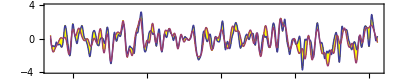

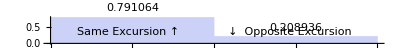

```mathematica
Window = 5;  
R = MeanFilter[MeanFilter[(1*MeanFilter[darwin[[All,2]],Window])-(1*MeanFilter[tahiti[[All,2]],Window]),Window-2],Window-4];
LNGTH=1600; STRT=12;
SOIT = Table[{1880+i/12, -R[[i]]},{i,STRT,LNGTH,1}];        (* scaled SOI Data Table from NCAR *)
 IC=52.5;  SHFT=0.95;
SOLN=NDSolve[{y''[x]+3.44*y[x]== -10.1*RHS[x+0.1], 
                               y'[IC]==-18.1, y[IC]==+4.8}, y, {x, -50, 260}]; 
SOIM=Table[{1880.0+x, 0.08*(First[y[x+SHFT] /. SOLN])},{x, STRT/12,LNGTH/12+0, 1/12}];   
OldCC = NewCC; NewCC = 100*Correlation[SOIT,SOIM][[2,2]];  Var = Variance[SOIT]-Variance[SOIM];
Print[{"= char t" 2*Pi/Sqrt[CF], "=err" Var[[2]]," .. " N[STRTY], N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{SOIT,SOIM},PlotRange->{-4,4},Frame->True,Axes->False, Filling->{1->{{2},Yellow}},  
              PlotLegends->{"SOI Data","SOIM"},AspectRatio->0.2]
SBIN = Abs[Sign[SOIT[[All,2]]]- Sign[SOIM[[All,2]]]]/2; 
Histogram[SBIN, Automatic, "Probability", LabelingFunction->Above, AspectRatio->0.05,  ChartLabels->Placed[{"Same Excursion ↑              ↓  Opposite Excursion"},Bottom]]
```